```mathematica
(*PARAMETERS OF THE HAMILTONIAN*)
Clear[L,upspins,downspins,dim];
L=9;
upspins=L /3;
downspins=L-upspins;
dim=L! /(upspins! downspins!);
(*Parameters for nearest-neighbor couplings*)
Jxy=1;
Jz=0.47;
alpha = 0.05;
(*Parameters for next-nearest-neighbor couplings*)
(*Set alpha=0 if NNN couplings do not exist*)
JJxy=1;
JJz=0;
(*BASIS*)
Clear[onebasisvector,basis];
onebasisvector=Flatten[{Table[1,{k,1,upspins}],Table[0,{k,1,downspins}]}];
basis=Permutations[onebasisvector];

(*elements of the Hamiltonian*)
(*Impurities and NN*)
Clear[HH];
Do[Do[HH[i,j]=0,{i,1,dim}],{j,1,dim}];

(*Diagonals*)
Do[
(*Ising interaction*)
Do[If[basis[[i,j]]==basis[[i,j+1]],HH[i,i]=HH[i,i]+Jz/4,HH[i,i]=HH[i,i]-Jz/4],
{j,1,L-1}],
{i,1,dim}]

(*Off DIagonals*)
Clear[howmany,site];
Do[
Do[
(*Initialization*)
	howmany=0;
	Do[site[kk]=0,{kk,1,L}];
	(*Sites where states i and j differ*)
		Do[If[basis[[i,k]] ≠  basis[[j,k]],{howmany=howmany+1,site[howmany]=k}];
		,{k,1,L}];
(*If only two neighbor sites differ,there is a coupling matrix element*)
	If[howmany ==2,If[site[2]-site[1]==1,{HH[i,j]=Jxy/2,HH[j,i]=Jxy/2}]];
	,{j,i+1,dim}];
	,{i,1,dim-1}];
Table[Table[HH[i,j],{i,1,dim}],{j,1,dim}]//MatrixForm;

(*Elements of H with NNN couplings*)
If[alpha>0,
(*Diagonal elements*)
Do[
(*Ising interactions*)
Do[If[basis[[i,j]]==basis[[i,j+2]],HH[i,i]=HH[i,i]+alpha JJz/4,HH[i,i]=HH[i,i]-alpha JJz/4],
{j,1,L-2}],
{i,1,dim}];
(*Off Diagonal Elements*)
(*Clear[howmany,site];*)
Do[
Do[
howmany=0;
Do[site[kk]=0,{kk,1,L}];
Do[If[basis[[i,k]]≠ basis[[j,k]],{howmany=howmany+1,site[howmany]=k}],
{k,1,L}];
If[howmany==2,
If[site[2]-site[1]==2,{HH[i,j]=alpha JJxy/2 , HH[j,i]=alpha JJxy/2}]],
{j,i+1,dim}],
{i,1,dim-1}]
]

(*Total H and diagonalisation*)
Clear[Hamiltonian,Energy,Vector];
Hamiltonian=Table[Table[HH[i,j],{i,1,dim}],{j,1,dim}];
Energy=Eigenvalues[Hamiltonian];
Vector=Eigenvectors[Hamiltonian];
```

```mathematica
(*PARAMETERS OF THE HAMILTONIAN*)
Clear[upspins,downspins];
upspins=(L /3)-1;
downspins=L-upspins;
Ldim=L! /(upspins! downspins!);
(*Parameters for nearest-neighbor couplings*)
Jxy=1;
Jz=0.5;
(*Parameters for next-nearest-neighbor couplings*)
(*Set alpha=0 if NNN couplings do not exist*)
JJxy=1;
JJz=0;
(*BASIS*)
Lonebasisvector=Flatten[{Table[1,{k,1,upspins}],Table[0,{k,1,downspins}]}];
Lbasis=Permutations[Lonebasisvector];

(*elements of the Hamiltonian*)
(*Impurities and NN*)
Clear[HH];
Do[Do[HH[i,j]=0,{i,1,Ldim}],{j,1,Ldim}];

(*Diagonals*)
Do[
(*Ising interaction*)
Do[If[Lbasis[[i,j]]==Lbasis[[i,j+1]],HH[i,i]=HH[i,i]+Jz/4,HH[i,i]=HH[i,i]-Jz/4],
{j,1,L-1}],
{i,1,Ldim}]

(*Off DIagonals*)
Clear[howmany,site];
Do[
Do[
(*Initialization*)
	howmany=0;
	Do[site[kk]=0,{kk,1,L}];
	(*Sites where states i and j differ*)
		Do[If[Lbasis[[i,k]] ≠  Lbasis[[j,k]],{howmany=howmany+1,site[howmany]=k}];
		,{k,1,L}];
(*If only two neighbor sites differ,there is a coupling matrix element*)
	If[howmany ==2,If[site[2]-site[1]==1,{HH[i,j]=Jxy/2,HH[j,i]=Jxy/2}]];
	,{j,i+1,Ldim}];
	,{i,1,Ldim-1}];
Table[Table[HH[i,j],{i,1,Ldim}],{j,1,Ldim}]//MatrixForm;

(*Elements of H with NNN couplings*)
If[alpha>0,
(*Diagonal elements*)
Do[
(*Ising interactions*)
Do[If[Lbasis[[i,j]]==Lbasis[[i,j+2]],HH[i,i]=HH[i,i]+alpha JJz/4,HH[i,i]=HH[i,i]-alpha JJz/4],
{j,1,L-2}],
{i,1,Ldim}];
(*Off Diagonal Elements*)
(*Clear[howmany,site];*)
Do[
Do[
howmany=0;
Do[site[kk]=0,{kk,1,L}];
Do[If[Lbasis[[i,k]]≠ Lbasis[[j,k]],{howmany=howmany+1,site[howmany]=k}],
{k,1,L}];
If[howmany==2,
If[site[2]-site[1]==2,{HH[i,j]=alpha JJxy/2 , HH[j,i]=alpha JJxy/2}]],
{j,i+1,Ldim}],
{i,1,Ldim-1}]
]

(*Total H and diagonalisation*)
LHamiltonian=Table[Table[HH[i,j],{i,1,Ldim}],{j,1,Ldim}];
LEnergy=Eigenvalues[LHamiltonian];
LVector=Eigenvectors[LHamiltonian];
```

```mathematica
(*PARAMETERS OF THE HAMILTONIAN*)
Clear[upspins,downspins];
upspins=(L /3)+1;
downspins=L-upspins;
Hdim=L! /(upspins! downspins!);
(*Parameters for nearest-neighbor couplings*)
Jxy=1;
Jz=0.5;
(*Parameters for next-nearest-neighbor couplings*)
(*Set alpha=0 if NNN couplings do not exist*)
JJxy=1;
JJz=0;
(*BASIS*)
Honebasisvector=Flatten[{Table[1,{k,1,upspins}],Table[0,{k,1,downspins}]}];
Hbasis=Permutations[Honebasisvector];

(*elements of the Hamiltonian*)
(*Impurities and NN*)
Clear[HH];
Do[Do[HH[i,j]=0,{i,1,Hdim}],{j,1,Hdim}];

(*Diagonals*)
Do[
(*Ising interaction*)
Do[If[Hbasis[[i,j]]==Hbasis[[i,j+1]],HH[i,i]=HH[i,i]+Jz/4,HH[i,i]=HH[i,i]-Jz/4],
{j,1,L-1}],
{i,1,Hdim}]

(*Off DIagonals*)
Clear[howmany,site];
Do[
Do[
(*Initialization*)
	howmany=0;
	Do[site[kk]=0,{kk,1,L}];
	(*Sites where states i and j differ*)
		Do[If[Hbasis[[i,k]] ≠  Hbasis[[j,k]],{howmany=howmany+1,site[howmany]=k}];
		,{k,1,L}];
(*If only two neighbor sites differ,there is a coupling matrix element*)
	If[howmany ==2,If[site[2]-site[1]==1,{HH[i,j]=Jxy/2,HH[j,i]=Jxy/2}]];
	,{j,i+1,Hdim}];
	,{i,1,Hdim-1}];
Table[Table[HH[i,j],{i,1,Hdim}],{j,1,Hdim}]//MatrixForm;

(*Elements of H with NNN couplings*)
If[alpha>0,
(*Diagonal elements*)
Do[
(*Ising interactions*)
Do[If[Hbasis[[i,j]]==Hbasis[[i,j+2]],HH[i,i]=HH[i,i]+alpha JJz/4,HH[i,i]=HH[i,i]-alpha JJz/4],
{j,1,L-2}],
{i,1,Hdim}];
(*Off Diagonal Elements*)
(*Clear[howmany,site];*)
Do[
Do[
howmany=0;
Do[site[kk]=0,{kk,1,L}];
Do[If[Hbasis[[i,k]]≠ Hbasis[[j,k]],{howmany=howmany+1,site[howmany]=k}],
{k,1,L}];
If[howmany==2,
If[site[2]-site[1]==2,{HH[i,j]=alpha JJxy/2 , HH[j,i]=alpha JJxy/2}]],
{j,i+1,Hdim}],
{i,1,Hdim-1}]
]

(*Total H and diagonalisation*)
HHamiltonian=Table[Table[HH[i,j],{i,1,Hdim}],{j,1,Hdim}];
HEnergy=Eigenvalues[HHamiltonian];
HVector=Eigenvectors[HHamiltonian];
```

```mathematica
RHS[state_,positionj_,positionk_]:=Module[{instate1=state,instate2=state},
instate1//Chop;
instate2//Chop;
instate1=applyhamexponent[-1,instate1,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];
instate1=applyupperorlower[0,positionk,instate1,L,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];
instate1=applyhamexponent[+1,instate1,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];
instate1=applyupperorlower[1,positionj,instate1,L,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];

instate2=applyupperorlower[1,positionj,instate2,L,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];
instate2=applyhamexponent[-1,instate2,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];
instate2=applyupperorlower[0,positionk,instate2,L,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];
instate2=applyhamexponent[1,instate2,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];

Return[instate2-instate1]
]
LHS[state_,positioni_,positionk_]:=Module[{instate1=state,instate2=state},

instate1//Chop;
instate2//Chop;
instate1=applyhamexponent[-1,instate1,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];
instate1=applyupperorlower[1,positionk,instate1,L,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];
instate1=applyhamexponent[+1,instate1,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];
instate1=applyupperorlower[0,positioni,instate1,L,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];

instate2=applyupperorlower[0,positioni,instate2,L,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];
instate2=applyhamexponent[-1,instate2,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];
instate2=applyupperorlower[1,positionk,instate2,L,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];
instate2=applyhamexponent[1,instate2,HEnergy,HVector,Hbasis,Energy,Vector,basis,LEnergy,LVector,Lbasis];

Return[Conjugate[instate1-instate2]]
]
```

```mathematica
(*Eigenvaluesquared=ConstantArray[{},L]
Time={};
Lyapt[tt_]:=Module[
{t=tt,LL2=ConstantArray[ConstantArray[0,L],L]},
Do[Do[LL2[[i,j]]=Sum[Conjugate[RHS[Vector[[3]],i,k]].RHS[Vector[[3]],j,k],{k,1,L}],{i,1,L}],{j,1,L}];
Return[Eigenvalues[LL2]]
]
Lyapattimes=Map[Lyapt[#]&,Range[1]/10]*)
```

```mathematica
tlist={};
list={};
Do[
LL2=ConstantArray[ConstantArray[0,L],L];
Clear[t];
t=(x/2);
tlist=Append[tlist,t];
Do[Do[LL2[[i,j]]=Sum[Conjugate[RHS[Vector[[3]],i,k]].RHS[Vector[[3]],j,k],{k,1,L}],{i,1,L}],{j,1,L}];
list=Append[list,Eigenvalues[LL2]]
,{x,0,48}]//AbsoluteTiming
Do[
LL2=ConstantArray[ConstantArray[0,L],L];
Clear[t];
t=(24+10x);
tlist=Append[tlist,t];
Do[Do[LL2[[i,j]]=Sum[Conjugate[RHS[Vector[[3]],i,k]].RHS[Vector[[3]],j,k],{k,1,L}],{i,1,L}],{j,1,L}];
list=Append[list,Eigenvalues[LL2]]
,{x,1,10}]//AbsoluteTiming
list=list//Chop;
```

{1568.04,Null}

{322.027,Null}

```mathematica
tlist+=(10)^-18
Singularv=Map[√#&,list];
Maxvalues=Map[Max[#]&,Singularv];
Minvalues=Map[Min[#]&,Singularv];
λlist=Map[Log[#]&,Singularv];
λlist/=tlist;
Maxλ=Map[Max[#]&,λlist];
Maxλ[[1]]=(Maxvalues[[2]]-Maxvalues[[1]])/(tlist[[2]]-tlist[[1]]);
Minλ=Map[Min[#]&,λlist];
Minλ[[1]]=(Minvalues[[2]]-Minvalues[[1]])/(tlist[[2]]-tlist[[1]]);
KS={};
Do[
tot=0;
Do[
If[λlist[[i,j]]>0,tot+=λlist[[i,j]]]
,{j,1,L}];
KS=Append[KS,tot]
,{i,1,Length[tlist]}]
KS;
```

{1/1000000000000000000,500000000000000001/1000000000000000000,1000000000000000001/1000000000000000000,1500000000000000001/1000000000000000000,2000000000000000001/1000000000000000000,2500000000000000001/1000000000000000000,3000000000000000001/1000000000000000000,3500000000000000001/1000000000000000000,4000000000000000001/1000000000000000000,4500000000000000001/1000000000000000000,5000000000000000001/1000000000000000000,5500000000000000001/1000000000000000000,6000000000000000001/1000000000000000000,6500000000000000001/1000000000000000000,7000000000000000001/1000000000000000000,7500000000000000001/1000000000000000000,8000000000000000001/1000000000000000000,8500000000000000001/1000000000000000000,9000000000000000001/1000000000000000000,9500000000000000001/1000000000000000000,10000000000000000001/1000000000000000000,10500000000000000001/1000000000000000000,11000000000000000001/1000000000000000000,11500000000000000001/1000000000000000000,12000000000000000001/1000000000000000000,12500000000000000001/1000000000000000000,13000000000000000001/1000000000000000000,13500000000000000001/1000000000000000000,14000000000000000001/1000000000000000000,14500000000000000001/1000000000000000000,15000000000000000001/1000000000000000000,15500000000000000001/1000000000000000000,16000000000000000001/1000000000000000000,16500000000000000001/1000000000000000000,17000000000000000001/1000000000000000000,17500000000000000001/1000000000000000000,18000000000000000001/1000000000000000000,18500000000000000001/1000000000000000000,19000000000000000001/1000000000000000000,19500000000000000001/1000000000000000000,20000000000000000001/1000000000000000000,20500000000000000001/1000000000000000000,21000000000000000001/1000000000000000000,21500000000000000001/1000000000000000000,22000000000000000001/1000000000000000000,22500000000000000001/1000000000000000000,23000000000000000001/1000000000000000000,23500000000000000001/1000000000000000000,24000000000000000001/1000000000000000000,34000000000000000001/1000000000000000000,44000000000000000001/1000000000000000000,54000000000000000001/1000000000000000000,64000000000000000001/1000000000000000000,74000000000000000001/1000000000000000000,84000000000000000001/1000000000000000000,94000000000000000001/1000000000000000000,104000000000000000001/1000000000000000000,114000000000000000001/1000000000000000000,124000000000000000001/1000000000000000000}

```mathematica
Minλ[[1]]
tlist//N
KS
```

-0.048182

{1.×10^-18,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.,20.5,21.,21.5,22.,22.5,23.,23.5,24.,34.,44.,54.,64.,74.,84.,94.,104.,114.,124.}

{1776.36,0.44293,0.661235,0.740213,0.774009,0.765015,0.724535,0.698255,0.674439,0.634326,0.601582,0.581225,0.555133,0.528431,0.510943,0.49301,0.472073,0.455994,0.442449,0.427517,0.414953,0.404182,0.392038,0.385784,0.382847,0.375313,0.362936,0.352795,0.348529,0.345387,0.339098,0.331636,0.326448,0.321041,0.31179,0.301812,0.294585,0.286634,0.276637,0.268913,0.263329,0.256056,0.248471,0.242954,0.2379,0.232708,0.228513,0.223623,0.217265,0.120044,0.089222,0.089075,0.0713761,0.055812,0.051423,0.049702,0.0422859,0.0381149,0.0366753}

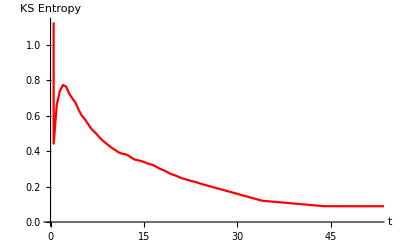

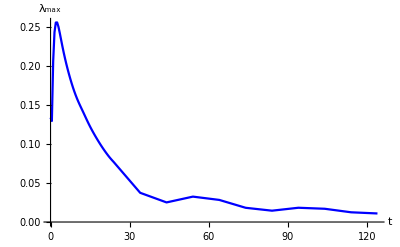

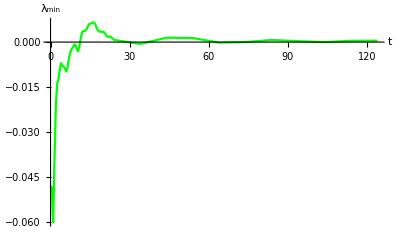

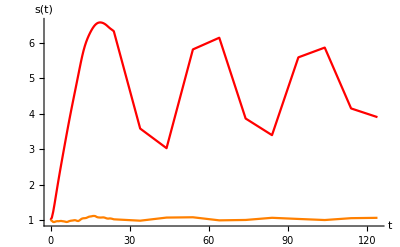

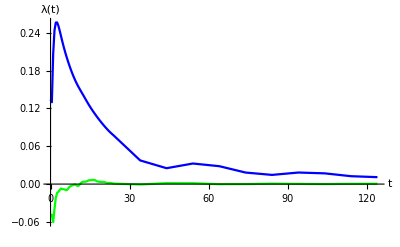

```mathematica
Singularvplot=ListLinePlot[Thread[{tlist,Maxvalues}],PlotRange-> All,AxesLabel->{"t","s_max"},AxesStyle->Directive[Black, 18],PlotStyle->{Red}];
KSplot=ListLinePlot[Thread[{tlist//N,KS}],AxesLabel->{"t","KS Entropy"},AxesStyle->Directive[Black, 18],PlotStyle->{Red}]
MinSingularvplot=ListLinePlot[Thread[{tlist,Minvalues}],PlotRange-> All,AxesLabel->{"t","s_min"},AxesStyle->Directive[Black, 18],PlotStyle->{Orange}];
MaxLambdaPlot=ListLinePlot[Thread[{tlist,Maxλ}],AxesLabel->{"t","λ_max"},AxesStyle->Directive[Black, 18],PlotStyle->{Blue},PlotRange-> All]
MinLambdaPlot=ListLinePlot[Thread[{tlist,Minλ}],AxesLabel->{"t","λ_min"},AxesStyle->Directive[Black, 18],PlotStyle->{Green},PlotRange-> All]
Show[Singularvplot,MinSingularvplot,PlotRange-> All,AxesLabel-> {"t","s(t)"}]
Lambdaplot=Show[MinLambdaPlot,MaxLambdaPlot,PlotRange-> All,AxesLabel-> {"t","λ(t)"}]
```

{aa→1.3591}

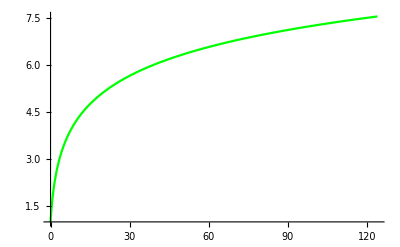

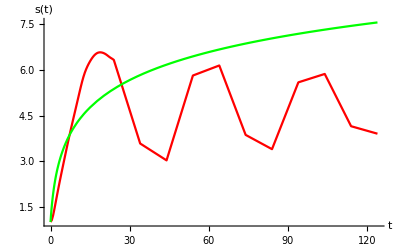

-Graphics-

```mathematica
DistTable = Table[{tlist[[j]],Maxvalues[[j]]},{j,1,Length[tlist]}];
lnparam=FindFit[DistTable,1+ aa Log[1+tt],aa,tt]
(*lnparam2=FindFit[DistTable,1+ aa √tt,aa,tt]
lnparam3=FindFit[DistTable,1+ aa Log[L,1+tt],aa,tt]*)
Plotfit=Plot[1+ aa Log[1+ tt]/.lnparam,{tt,0,tlist[[-1]]},PlotStyle-> {Green}]
(*Plotfit2=Plot[1+ aa √tt/.lnparam2,{tt,0,tlist[[-1]]},PlotStyle-> {Purple}]
Plotfit3=Plot[1+ aa Log[L,1+ tt]/.lnparam3,{tt,0,tlist[[-1]]},PlotStyle-> {Orange}]*)
Singmaxfit=Show[Singularvplot,Plotfit,PlotRange-> All,AxesLabel-> {"t","s(t)"}]
Singminmax=Show[Singularvplot,MinSingularvplot,PlotRange-> All,AxesLabel-> {"t","s(t)"}]
```

```mathematica
Export["Singmaxfit;fit="<>ToString[aa/.lnparam]<>";L="<>ToString[L]<>";Up="<>ToString[upspins]<>";Jxy="<>ToString[Jxy]<>";Jz="<>ToString[Jz]<>";JJxy="<>ToString[JJxy]<>";JJz="<>ToString[JJz]<>";a="<>ToString[alpha]<>";tin"<>ToString[tlist[[2]]//N]<>"to"<>ToString[tlist[[-1]]//N]<>".png",Singmaxfit,OverwriteTarget->True];
Export["Singminmax;L="<>ToString[L]<>";Up="<>ToString[upspins]<>";Jxy="<>ToString[Jxy]<>";Jz="<>ToString[Jz]<>";JJxy="<>ToString[JJxy]<>";JJz="<>ToString[JJz]<>";a="<>ToString[alpha]<>";tin"<>ToString[tlist[[2]]//N]<>"to"<>ToString[tlist[[-1]]//N]<>".png",Singminmax,OverwriteTarget->True];
Export["Lambdaplot;L="<>ToString[L]<>";Up="<>ToString[upspins]<>";Jxy="<>ToString[Jxy]<>";Jz="<>ToString[Jz]<>";JJxy="<>ToString[JJxy]<>";JJz="<>ToString[JJz]<>";a="<>ToString[alpha]<>";tin"<>ToString[tlist[[2]]//N]<>"to"<>ToString[tlist[[-1]]//N]<>".png",Lambdaplot,OverwriteTarget->True];
Export["KSplot;L="<>ToString[L]<>";Up="<>ToString[upspins]<>";Jxy="<>ToString[Jxy]<>";Jz="<>ToString[Jz]<>";JJxy="<>ToString[JJxy]<>";JJz="<>ToString[JJz]<>";a="<>ToString[alpha]<>";tin"<>ToString[tlist[[2]]//N]<>"to"<>ToString[tlist[[-1]]//N]<>".png",KSplot,OverwriteTarget->True];
Export["KS;L="<>ToString[L]<>";Up="<>ToString[upspins]<>";Jxy="<>ToString[Jxy]<>";Jz="<>ToString[Jz]<>";JJxy="<>ToString[JJxy]<>";JJz="<>ToString[JJz]<>";a="<>ToString[alpha]<>";tin"<>ToString[tlist[[2]]//N]<>"to"<>ToString[tlist[[-1]]//N]<>".csv",KS,OverwriteTarget->True];
Export["Singularv;L="<>ToString[L]<>";Up="<>ToString[upspins]<>";Jxy="<>ToString[Jxy]<>";Jz="<>ToString[Jz]<>";JJxy="<>ToString[JJxy]<>";JJz="<>ToString[JJz]<>";a="<>ToString[alpha]<>";tin"<>ToString[tlist[[2]]//N]<>"to"<>ToString[tlist[[-1]]//N]<>".csv",Singularv,OverwriteTarget->True];
```

```mathematica
D[Log[1+l],l]
```

1/(1+l)

```mathematica
(Maxvalues[[2]]-Maxvalues[[1]])/(tlist[[2]]-tlist[[1]])
```

0.134102

```mathematica
list
```

{{1.,1.,1.,1.,1.,1.,1.,1.,1.},{1.1386,1.12342,1.10073,1.06593,1.03417,1.00335,0.97504,0.955135,0.952398},{1.51173,1.4204,1.32038,1.19717,1.09667,1.00815,0.940177,0.898304,0.886646},{2.07758,1.82595,1.57441,1.32401,1.146,1.01665,0.947649,0.888818,0.888525},{2.78651,2.2741,1.80231,1.41649,1.19006,1.08794,1.05561,0.917686,0.917054},{3.60254,2.73108,1.9894,1.48687,1.26042,1.1562,1.08074,0.937401,0.93269},{4.50213,3.18099,2.13716,1.56071,1.33325,1.16032,1.04554,0.935355,0.928367},{5.47216,3.61525,2.24845,1.63697,1.39003,1.18303,1.10789,0.944647,0.93758},{6.50969,4.03219,2.32841,1.69587,1.4547,1.24097,1.17802,0.951993,0.945464},{7.61834,4.42946,2.382,1.74707,1.51699,1.25092,1.13158,0.950255,0.930249},{8.80316,4.80103,2.41664,1.81483,1.54426,1.24167,1.15317,0.93256,0.921751},{10.0664,5.1383,2.44433,1.90352,1.53215,1.29814,1.24916,0.950902,0.907315},{11.4049,5.43349,2.47568,1.99121,1.52371,1.3587,1.23619,0.976613,0.888474},{12.809,5.68628,2.52353,2.05224,1.55473,1.3481,1.21751,0.961395,0.897441},{14.2661,5.90041,2.59668,2.07643,1.60842,1.33019,1.31632,0.943275,0.928884},{15.7659,6.07605,2.6938,2.07085,1.65561,1.3604,1.35269,0.955307,0.951071},{17.3055,6.20982,2.82094,2.05823,1.68647,1.38323,1.31001,0.968117,0.962108},{18.8893,6.30057,2.97991,2.06065,1.69676,1.37166,1.36753,0.984214,0.970797},{20.5259,6.35336,3.15457,2.09639,1.69568,1.4381,1.36743,0.992269,0.985556},{22.226,6.37788,3.32183,2.1695,1.70378,1.40033,1.38287,0.983334,0.982055},{24.0003,6.38465,3.45305,2.25146,1.74267,1.4045,1.37873,0.972185,0.952074},{25.8549,6.3861,3.52051,2.29444,1.78426,1.45036,1.40675,0.976755,0.938814},{27.7793,6.40457,3.51789,2.27576,1.79888,1.52223,1.42099,1.00467,0.974874},{29.7301,6.4721,3.47416,2.2263,1.8091,1.58381,1.52579,1.05865,1.03616},{31.627,6.61359,3.44193,2.20712,1.85906,1.69832,1.62217,1.11132,1.08161},{33.3793,6.82828,3.46147,2.25103,1.899,1.73816,1.63237,1.1306,1.09833},{34.9313,7.09239,3.5352,2.33037,1.90982,1.61772,1.59318,1.13233,1.10199},{36.2834,7.38347,3.64108,2.40115,1.91004,1.55411,1.5302,1.15573,1.11457},{37.4725,7.69416,3.76318,2.45917,1.92236,1.59894,1.52778,1.20342,1.14771},{38.5387,8.01785,3.89571,2.51499,1.94747,1.67987,1.55284,1.22722,1.18608},{39.51,8.33869,4.02698,2.53982,1.96697,1.70386,1.56851,1.22827,1.20353},{40.3992,8.64322,4.14171,2.52401,2.00406,1.7019,1.55394,1.2417,1.21406},{41.1983,8.92927,4.23141,2.50779,2.07155,1.74867,1.55259,1.27043,1.23399},{41.8846,9.19751,4.28974,2.52714,2.12965,1.79454,1.58181,1.27487,1.23995},{42.4396,9.44322,4.31323,2.58636,2.13762,1.77518,1.56886,1.23043,1.2266},{42.856,9.65882,4.3135,2.66356,2.11628,1.762,1.52437,1.21644,1.17665},{43.1311,9.83924,4.31379,2.7255,2.09043,1.78341,1.55537,1.2111,1.15123},{43.2677,9.98671,4.33042,2.74886,2.06359,1.76609,1.58756,1.18638,1.14296},{43.2812,10.1116,4.36455,2.73649,2.0378,1.71227,1.52553,1.15985,1.13916},{43.1938,10.228,4.40777,2.7051,2.02122,1.68816,1.50679,1.1576,1.14407},{43.0202,10.3464,4.45004,2.67951,2.01567,1.66834,1.58157,1.15606,1.15035},{42.7642,10.4683,4.48646,2.67199,2.01148,1.63449,1.58609,1.14004,1.13633},{42.4276,10.5845,4.51944,2.6875,1.98699,1.6394,1.53479,1.12977,1.10542},{42.0224,10.6768,4.55165,2.72173,1.98704,1.65727,1.53703,1.13211,1.08137},{41.5833,10.7249,4.57735,2.76048,2.01428,1.64321,1.55916,1.12153,1.07795},{41.1641,10.7167,4.58645,2.78707,2.03783,1.68635,1.53054,1.09283,1.08931},{40.8017,10.6568,4.57282,2.79521,2.04504,1.81196,1.50855,1.09616,1.07882},{40.467,10.5632,4.53676,2.79471,2.04564,1.88579,1.53514,1.07831,1.06013},{40.065,10.4548,4.48755,2.79148,2.04134,1.82919,1.58285,1.05213,1.03638},{12.8243,9.55584,4.28584,2.54629,1.68371,1.36623,1.13926,1.00113,0.958191},{9.16365,5.54984,3.99055,2.48488,1.79722,1.4954,1.42913,1.16543,1.13836},{33.8336,5.6855,4.33496,2.48646,1.96728,1.69599,1.57307,1.1966,1.15687},{37.7793,6.94778,4.44196,2.36983,1.86723,1.42385,1.24314,1.01672,0.977333},{14.9359,7.07412,4.08634,2.19887,1.81748,1.48676,1.4443,1.04362,0.999314},{11.527,7.41907,3.91037,2.63138,1.75251,1.6773,1.64315,1.18148,1.12476},{31.275,9.31841,3.83862,2.31664,1.78843,1.58975,1.36157,1.07741,1.05742},{34.4385,7.70004,3.75217,2.22884,1.80141,1.35803,1.21018,1.0059,0.995215},{17.2197,7.06445,3.70579,2.31655,1.80531,1.54715,1.53322,1.20531,1.10279},{15.2385,8.9746,4.18487,2.23789,1.95008,1.71283,1.56124,1.18835,1.1232}}

```mathematica
Map[Max[#]&,list]
```

{1.,1.1386,1.51173,2.07758,2.78651,3.60254,4.50213,5.47216,6.50969,7.61834,8.80316,10.0664,11.4049,12.809,14.2661,15.7659,17.3055,18.8893,20.5259,22.226,24.0003,25.8549,27.7793,29.7301,31.627,33.3793,34.9313,36.2834,37.4725,38.5387,39.51,40.3992,41.1983,41.8846,42.4396,42.856,43.1311,43.2677,43.2812,43.1938,43.0202,42.7642,42.4276,42.0224,41.5833,41.1641,40.8017,40.467,40.065,12.8243,9.16365,33.8336,37.7793,14.9359,11.527,31.275,34.4385,17.2197,15.2385}

```mathematica
Eigenvalues[LL2]//AbsoluteTiming
```

{0.0000544,{15.2385,8.9746,4.18487,2.23789,1.95008,1.71283,1.56124,1.18835,1.1232}}

```mathematica
Clear[t]
LL2=ConstantArray[ConstantArray[0,L],L]
t=2;
Do[Do[LL2[[i,j]]=Sum[Conjugate[RHS[Vector[[3]],i,k]].RHS[Vector[[3]],j,k],{k,1,L}],{i,1,L}],{j,1,L}];
Eigenvalues[LL2]//AbsoluteTiming
```

{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

{0.0000413,{2.78651,2.2741,1.80231,1.41649,1.19006,1.08794,1.05561,0.917686,0.917054}}

```mathematica
(*t1*)
{0.0019677,{3.414428134003208,3.1547957708518672,2.3406620018585533,2.05798041678658,1.5087858727199215,1.236400156913963,0.9897624465964732,0.9417728976501467,0.8705423467792808}}
```

{0.0019677,{3.41443,3.1548,2.34066,2.05798,1.50879,1.2364,0.989762,0.941773,0.870542}}

```mathematica
(*t2*)
{0.0000917,{6.203808973385473,5.523366346548679,3.7640497144835807,2.878588620466977,2.0072310597167844,1.5320242076384862,1.019819813880751,0.9108894209764102,0.8606943568529779}}
```

{0.0000917,{6.20381,5.52337,3.76405,2.87859,2.00723,1.53202,1.01982,0.910889,0.860694}}

```mathematica
t
```

2

```mathematica
Range[10]/10
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}